```mathematica
Quit[];
(*Built on RHPackage by Sheehan Olver, https://github.com/dlfivefifty/RHPackage*)
```

```mathematica
(* Make sure the directory with the "ISTPackage" and "RiemannHilbert" folders in in the path *)
AppendTo[$Path,FileNameJoin[{NotebookDirectory[],"istpackage"}]];
(*or, for example*)
(*AppendTo[$Path,"~/Dropbox/istpackage"];*)
<<RiemannHilbert`;
<<ISTPackage`;
```

## Initializing our parameters

```mathematica
matrixexp[α_]:=({{Exp[α], 0}, {0, Exp[-α]}});
Q=(1/Sqrt[2])({{1, 1}, {-1, 1}});
```

## Define a list of the segments

```mathematica
sg1={Line[{1+I,-1+I}],Line[{-1+I,-1-I}],Line[{-1-I,1-I}],Line[{1-I,1+I}]};
```

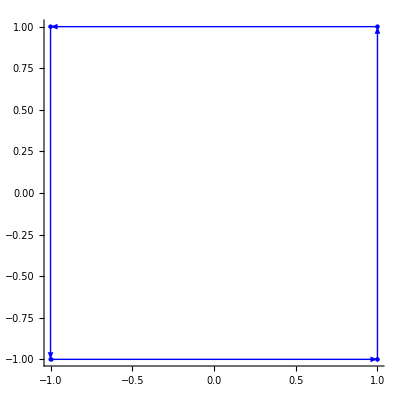

```mathematica
DomainPlot[sg1]
```

## Define jump matrices and list of jumps for the PIII universality class

```mathematica
GΣ1[x_,t_][z_]:=matrixexp[-I(x z+t z^2+2/z)].Q.matrixexp[I(x z+t z^2+2/z)];

J[x_,t_,bigN_]:={{GΣ1[x,t][#]&,GΣ1[x,t][#]&,GΣ1[x,t][#]&,GΣ1[x,t][#]&},sg1,{2*bigN,2*bigN,2*bigN,2*bigN}};
```

### NLS Routine

```mathematica
qNLS//Clear;
qNLS[x_,t_,nn_]:=qNLS[x,t,nn]=Module[{eeθ},
rhp2=J[x,t,nn]//MakeListFun;
eeθ={{1,0},{0,1}};
u2= RHSolve[rhp2];
dom = u2//DomainPlot;
out2 = -(DomainIntegrate[u2])[[1,2]]/(Pi );
out2
];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.853553+0.306849 ⅈ,-3.04853×10^-18-0.109847 ⅈ,-1.7275×10^-17-0.0418837 ⅈ,-7.11324×10^-18-0.0328788 ⅈ,«44»,0.00159639-0.00109359 ⅈ,0.00144949-0.00106427 ⅈ,«190»},«49»,«190»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.853553+0.306849 ⅈ,-3.04853×10^-18-0.109847 ⅈ,-1.7275×10^-17-0.0418837 ⅈ,-7.11324×10^-18-0.0328788 ⅈ,«44»,0.00159639-0.00109359 ⅈ,0.00144949-0.00106427 ⅈ,«190»},{«23»+«21» ⅈ,«49»,«190»},«47»,{«1»},«190»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.853553+0.306849 ⅈ,-3.04853×10^-18-0.109847 ⅈ,-1.7275×10^-17-0.0418837 ⅈ,-7.11324×10^-18-0.0328788 ⅈ,«44»,0.00159639-0.00109359 ⅈ,0.00144949-0.00106427 ⅈ,«190»},«49»,«190»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

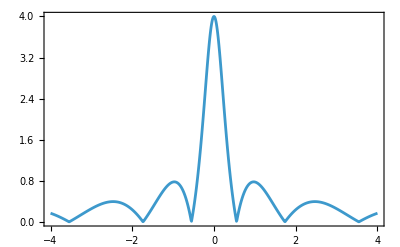

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\RHP_PIII.csv

```mathematica
data = Table[{xx,Abs[qNLS[xx,0,15]]},{xx,-4,4,.01}];
testplot = ListPlot[data,Joined->True,PlotRange->All,Axes->False,Frame->True];
Print[testplot];
fileName="RHP_PIII.csv";
path=FileNameJoin[{NotebookDirectory[],fileName}];
Export[path,data];
Print["Exported: ",path];
```

## Define jump matrices and list of jumps for the PV universality class

```mathematica
ζ=0.3;
nu = 4;
μD=Sqrt[2]*Gamma[(nu+1)/2]/Gamma[nu/2];
GΣ1[x_,t_][z_]:=matrixexp[-I(x z+t z^2+μD/ζ Log[(z+ζ)/z])].Q.matrixexp[I(x z+t z^2+μD/ζ Log[(z+ζ)/z])];

J[x_,t_,bigN_]:={{GΣ1[x,t][#]&,GΣ1[x,t][#]&,GΣ1[x,t][#]&,GΣ1[x,t][#]&},sg1,{2*bigN,2*bigN,2*bigN,2*bigN}};
```

3.75994

### NLS routine

```mathematica
qNLS//Clear;
qNLS[x_,t_,nn_]:=qNLS[x,t,nn]=Module[{eeθ},
rhp2=J[x,t,nn]//MakeListFun;
eeθ={{1,0},{0,1}};
u2= RHSolve[rhp2];
dom = u2//DomainPlot;
out2 = -(DomainIntegrate[u2])[[1,2]]/(Pi );
out2
];
```

### Data generation for PV

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.853553+0.306849 ⅈ,-4.46169×10^-19-0.109847 ⅈ,-1.62828×10^-17-0.0418837 ⅈ,-6.33432×10^-18-0.0328788 ⅈ,-2.53311×10^-18-0.0217561 ⅈ,«42»,0.00173573-0.00110009 ⅈ,0.00159639-0.00109359 ⅈ,0.00144949-0.00106427 ⅈ,«190»},{«1»},«47»,{«1»},«190»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.853553+0.306849 ⅈ,-3.04853×10^-18-0.109847 ⅈ,-1.7275×10^-17-0.0418837 ⅈ,-7.11324×10^-18-0.0328788 ⅈ,-3.04853×10^-18-0.0217561 ⅈ,«42»,0.00173573-0.00110009 ⅈ,0.00159639-0.00109359 ⅈ,0.00144949-0.00106427 ⅈ,«190»},{«1»},«47»,{«1»},«190»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

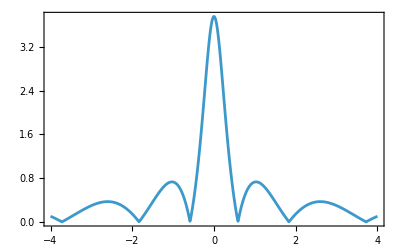

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\RHP_PV.csv

```mathematica
data = Table[{xx,Abs[qNLS[xx,0,15]]},{xx,-4,4,.01}];
testplot = ListPlot[data,Joined->True,PlotRange->All,Axes->False,Frame->True];
Print[testplot];
fileName="RHP_PV.csv";
path=FileNameJoin[{NotebookDirectory[],fileName}];
Export[path,data];
Print["Exported: ",path];
```